```mathematica
jan={0.2,-1.8,-8.6,-7.2,0.9,-4.1,-2.7,1.4,-9.4,-5.5,-2.1,-1.1,-5.2,-0.1,1.8,1.2,-9.3,-3.6,-4.6,-2.9,-5.4,-3.3,-7.7,0.9,-3.5,-1.6,-4.5,-3.6,-1.2,-3.8,-1.8,0.3,-5.1,-6,-7.9,-1.3,-5.8,-2.5,-5.2,0.9,-4.1,-3.2,-3.6,-1.6,-3.6,-0.5,-3.4,-1,-4.1,-2.3,-1.5,-1.8,-1.4,-5.4,-3.2,-3.6,-4.7,-1.9,-8.1,-5.7,-1.5,-3.3,-1.8,-5.7,-0.7,-4,0.5,-3.8,-1.7,-3.1,-4.5,1.6,-3.5,1,-2.4,0,-2.5,-1.6,-1.7,-1.5,-1.5,-7.4,-10.9,-11.2,-3.8,-1.9,-2.7,-2.5,-4.3,-5.4,-0.1,-5,-3.4,-1.8,-3.2,-4.8,-3.4,-4.6,-0.5,-4.1,-4.4,-4.6,-2.7,-2,-7.7,-2,-2,-7.3,-5.3,-7,-3,-7.6,-1.2,-3.8,0.7,0.2,1.1,-5.1,-2.2,-1.5,-7.1,-4.7,-4,-7.2,0.7,-3,-9,-5,-12,-0.1,2.4,0.5,-0.7,0.6,-0.3,-2.1,-2.5,-4,-2.3,-0.3,-2.3,-1,-0.7,-1.1,-3.9,-3.5,0.6,-3.1,-0.3,1.4,-1.9,-7.8,-2.6,-1.7,-4,-2.2,0.1,-5,-1,-0.6,-2.5,3.3};
feb={0.1,-6.2,-1.3,-6.8,0.9,-1.6,-8.8,-3,-2,-1.5,-0.5,-7.1,-12.2,-1.5,-2.4,-1.3,-5.9,-4.3,-5.5,-0.5,-7,-0.9,-8,-1.3,-1.3,-1.5,-1.5,-3.8,-0.6,-7.6,-7.2,-1.9,-0.5,-4.9,-11,-0.7,-8.2,-0.8,-4.2,-2.2,-2.5,-7.6,-6.7,-5,0.5,-4.9,-1.4,-1.2,-3,-1.6,-5.2,-0.2,-2.1,-4.2,-0.5,1.4,-2.1,-2.4,-5.2,-2.1,-4.6,0.3,-1.9,-4.5,-5.7,-6.9,0.5,-5,-2.1,-2.5,-9.1,-1.9,-3.8,-2.9,-3.6,0.1,-1.2,-5.1,-3.5,0.4,1.6,-10.8,-6.6,-11.1,1.3,-1.5,-1.1,-5.1,-10.7,-3.3,0.8,-1.7,-1.9,-2.4,-4.3,-6,-5.2,-9.2,-1.6,-6.7,-1.6,-5.2,0.4,-2.8,-7.8,-4.3,-4.7,-10.9,-1.6,-4,-6,-10.7,-1.9,-1,-0.7,0.6,-1.2,-2.1,-5,-6.3,-6.2,-6.2,-2.7,-4,-3.8,-1.7,-11.6,-8.4,-4.4,-0.9,2.4,3.4,-3.1,-0.1,-0.9,-6.9,0.1,-6.9,-0.5,0.8,-2.4,-0.4,-4.2,0.9,-4,-1.6,-2.5,-3.5,-3.6,2.1,-2.6,-6.1,-5.1,-3.7,-2.1,1.5,0.4,-0.3,-0.7,-4.1,1,2};
mar={0.7,-2.7,-0.2,-4.4,-0.2,-1.9,-4.2,-5.8,-5,0.1,-2.1,-2.3,1.8,-0.9,-0.6,-0.5,-3,-2.1,-4.9,-1.1,-3.1,-0.6,-6.2,1.2,-4.4,0.3,-1,-3,-0.3,-8.9,-4.3,0.4,-2.4,-2,-0.5,2.8,-2.8,0.1,-1.8,-1.3,-3.5,-2.9,-2,-2.8,3.4,-2.1,0.2,-2,0.1,-2.1,-2.3,1.3,0.2,1.2,1.8,-0.7,-4,-2.8,-6,-0.1,-2.3,2.9,3.4,-1.5,-0.5,-3.9,-2.7,-0.4,1.4,-2,0.2,0.6,-4.3,-2.6,0.8,0.2,-0.4,0.3,-2.3,3.6,-0.4,-5.5,-3.1,-7.2,2.4,-1.1,1.3,-1.4,-5.1,1.7,-0.6,0.9,-3.5,-3.7,2.6,0,-3.5,-1.6,-2.3,-5.5,2.2,-1.5,3,-4.1,-4.4,-2.3,-1.4,-1.3,2.6,0.8,-4,-1.6,-2.8,0.2,2.9,0.8,0.9,-2.9,0.4,-1.6,-1.1,-3.1,-2.2,1.1,-0.1,-2,-1.7,0.2,-4.2,-2.1,2.6,3.9,1.4,2,1,-0.1,1.3,-1.5,1.6,-0.5,0.7,1.2,-1.3,1.6,2.3,0.9,-2.3,-3.8,3.8,0.8,0.1,-1.1,0.3,3.5,-3.2,3.6,3,2.3,2.4,-2.5,1.8,2.7};
apr={2.2,3.4,2.2,2.9,3.8,2.3,4.3,3.9,0.5,3.4,5.8,5.4,0.6,3.9,2.4,3.6,1.3,3.7,-0.2,5,1,4,0.5,3.6,2.5,2.3,3.7,4.5,3.9,-0.3,2.1,3.7,2.6,2.9,4,5.9,4,3.4,3.7,1.9,3.3,2.6,3.9,0.4,2.6,3.8,1.7,5.2,2.3,2.5,1.3,4.7,4,3.2,4.7,6.4,3.9,4.8,0.6,3.7,3.1,4.9,6.7,1.6,1.9,1.2,5.6,3.3,2.6,3.5,0.6,5.1,1.4,3.3,3.2,5.2,4.3,3.2,4.8,4.3,4.6,2.3,1.2,3.8,6.4,2.3,4.8,5.7,4.6,6.1,5.1,5.2,4.1,5.9,5.9,2.4,1,0.8,3.1,1.8,5.1,3.4,5.1,4.1,3.3,5.2,3.2,0.7,4.2,6.4,3.9,1.7,2.7,3.1,3.1,5.4,3.8,3.5,2.3,2.6,2.8,4.8,3.9,4.1,4,5.3,1.6,2.1,4.1,3.1,4.6,6.5,4.8,2.6,5.2,5.9,3.3,5.6,3.1,3.1,6.6,6,5,6.5,3.7,6,6,4.5,7.3,6.5,7.6,5.5,8.3,4,4,6.6,6.5,5.3,4,6.2,6.5,6.2};
maj={9.7,7.4,5.9,10.2,8.1,5.1,10.8,7,3.4,10.4,7.4,8.9,6.2,10.3,5.8,6.3,9.8,5.6,5.6,8.7,8.5,8.4,7.8,9.4,8.8,7.6,6.4,8.7,8.7,7.5,11.9,11,8.8,8.2,7.1,9,11.7,8.2,10.2,8.7,7,6.8,10.1,5.8,9.2,7.1,9.7,10.6,7.2,7.8,5.2,9.7,10.5,7.2,9.5,9,7.4,7.9,8.6,9.6,9.8,10.3,12.4,9.7,7.4,8.7,9.5,8,5.6,7.8,8.9,10.3,9.4,8.8,7.6,11.2,7.2,9.3,12.2,8.9,9.1,10.2,7.8,7.5,10.5,7.8,8.6,9.1,11.9,9.8,11.5,10.4,7.2,7.7,9.3,10.4,6.6,10.3,7.9,8.6,9.5,10.1,8.6,7.3,11.3,10.8,7.4,9.4,8,7.3,8.1,8.9,10.4,8.8,9.7,8.2,10.3,9.7,8.9,8.9,9.8,7.8,10.8,9.4,10.2,10.9,9,11.5,7.5,11.2,11.5,10.8,7.2,12.6,12.6,8.6,8.1,7.6,8.2,9.8,8.9,11.1,9.9,11.4,10.3,9.6,9.7,10.1,10.2,10.7,10.7,10.1,10.6,10.9,11.9,9.9,8.9,11.9,10.1,14.8,9.6,8.8};

dec={-3.2,-5.3,0.1,-1.8,-0.5,-0.6,1,-2.6,-7.6,-1,-0.8,-7.2,-2.9,-1.7,0.1,-5.5,-4.6,-7.4,0.5,-3,-3.6,-4.2,0.6,-4,-1.5,-2,-1.6,-2.3,-2.8,0.5,-1.5,-3,0,-4.6,0.2,0.3,-1.7,-1.8,0.3,0.1,-2.4,-1.1,-3.7,-4.4,-0.6,-2.2,0,-2.4,-3.3,-0.8,-1,0.3,1.4,1.8,-2.1,2.2,-7,-0.7,-2.4,-1.2,-3.3,-0.9,-1,-0.5,-3.9,2.4,-4.5,-2.9,-5.5,-1.2,3,0.8,-1.8,2.3,-3.1,2.6,0.2,2.7,-3.9,-0.5,-2.8,-2.7,-2.7,-0.1,0.3,1.4,-1.4,-0.3,-2,2.3,1,-1.1,2,-1.7,1.9,1.6,-3.2,-0.3,-0.9,-1.6,-0.1,1.2,-3.4,-3.2,-1.8,-0.9,-4,-0.4,-4.6,-1.5,-4,-0.8,1.1,3.3,-2.5,1.2,0.7,-2.6,-0.1,-6,-1.7,-0.8,-5.7,0.3,-1.1,0.8,-4.3,-1.5,-1.5,-2.4,-2.2,0.8,0.6,1,-0.4,1.8,-4.9,-3.2,-0.5,-0.4,-1.6,2.3,-2,-4,0.9,1,-0.5,4.3,1.2,0.9,-2,-7.2,1.9,-3.6,2.8,-0.1,3.5,1.6,0.9,0.2,2.4,3.4};
```

```mathematica
Total[Flatten[{dec,jan,feb}]]/Length[Flatten[{dec,jan,feb}]]
```

-2.48313

```mathematica
Total[Flatten[{mar,apr,maj}]]/Length[Flatten[{mar,apr,maj}]]
```

3.97922

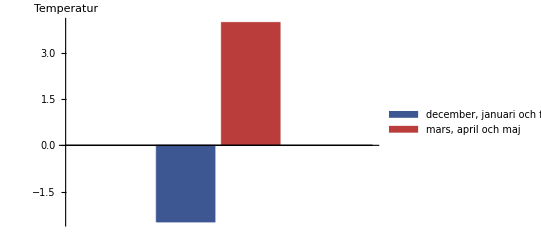

```mathematica
BarChart[{-2.4831275720164614, 3.9792181069958854},ChartLegends->{"december, januari och februari", "mars, april och maj"},ChartStyle->"DarkRainbow", ChartLegends->Automatic, AxesLabel->{"", "Temperatur"}]
```